# Water in a Barrel

"THE CHALLENGE"

Write code to determine the volume of water in a cylindrical barrel lying on its side, given the radius R and length L of the cylinder and height h of water within the barrel.

## More Details

Here is a cylindrical barrel of radius R=D/2 and length L, filled with water up to height h:

-Graphics-

Words that may help in this challenge include sagitta and apothem.

## What Your Code Should Do

Write a function WaterInBarrel that takes the inputs R, L, h and outputs the volume of water.

```mathematica
WaterInBarrel[1,2,1]
```

π

```mathematica
WaterInBarrel[6.,4.,5.]
```

178.418

"SCRATCH AREA"

```mathematica
CircleArea[R_?NumericQ, sagitta_?NumericQ]:=2R^2 Integrate[ Sqrt[1-y^2],{y,-1,sagitta/R-1}]
```

```mathematica
CircleArea[2,4]
```

4 π

```mathematica
sagitta = 2.71
R = 6.71
```

2.71

6.71

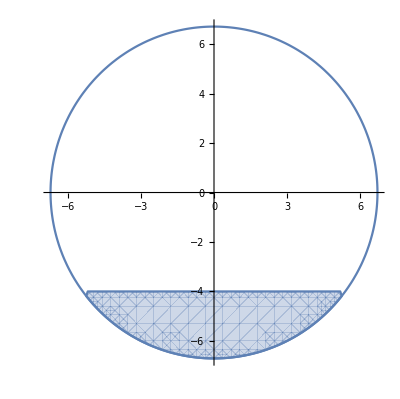

```mathematica
Show[ParametricPlot[{R*Cos[t],R*Sin[t]},{t,0,2*Pi}],RegionPlot[y<=Min[sagitta-R, Sqrt[R^2-x^2]]&&y>=-Sqrt[R^2-x^2],{x,-R,R},{y,-R,R}],PlotRange->All]
```

```mathematica
WaterInBarrel[R_,L_,h_]/;0≤h≤2R&&L≥0:= 2L NIntegrate[ R Sqrt[1-(y/R)^2],{y,-R,h-R}]
```

```mathematica
WaterInBarrel[1.6,7.5,2]
```

39.6583

```mathematica
WaterInBarrel[1.9,1.6,2.92]
```

14.9622

```mathematica
Integrate[Sqrt[1 - x^2], {x, -1, a-1}]
```

ConditionalExpression[1/2 ((-1+a) √(-((-2+a) a))+π-2 ArcCot[a/(√(-((-2+a) a)))]), Re[a]≤2||a∉ℝ]

```mathematica
WaterInBarrel[R_,L_,h_]/;0≤h≤2R&&L≥0:=  With[{a=h/R},
L R^2Sqrt[(-a+2)a](a+1) + ArcCos[1-a]]
```

```mathematica
WaterInBarrel[1.6,7.5,2]
```

39.6583

```mathematica
WaterInBarrel[R_,L_,h_]/;0≤h≤2R&&L≥0:= 2L NIntegrate[ R Sqrt[1-(y/R)^2],{y,-R,h-R}, WorkingPrecision->20]
```

```mathematica
WaterInBarrel[1.6,7.5,2]
```

NIntegrate::precw: The precision of the argument function (1.6 √(1-0.390625 y^2)) is less than WorkingPrecision (20.).

```mathematica
39.658330388638824
```

39.6583

```mathematica
WaterInBarrel[R_,L_,h_]:=NIntegrate[(1-y^2)^.5{y,-1,h/R-1}2L R^2,20]
```

```mathematica
WaterInBarrel[1.6,7.5,2]
```

NIntegrate::precw: The precision of the argument function (1.6 √(1-0.390625 y^2)) is less than WorkingPrecision (20.).

39.6583

"ENTER YOUR CODE HERE"

```mathematica
WaterInBarrel[R_,L_,h_]:=2L R^2NIntegrate[(1-y^2)^.5{y,-1,h/R-1},20]
```